# Max Ring Currents

```mathematica
J [r_]:=r*(1-r)*(1+2*r/(r^2-r+1)+r^2/((r^2-r+1)^2));
J11[r_]:= r(1-r);
J12[r_]:= r^2(1-r^2/(r^2-r+1));
J21[r_]:= r^2/(r^2-r+1)*(1-r);
J22[r_]:= r^2/(r^2-r+1)*(1-r^2/(r^2-r+1))*r;
```

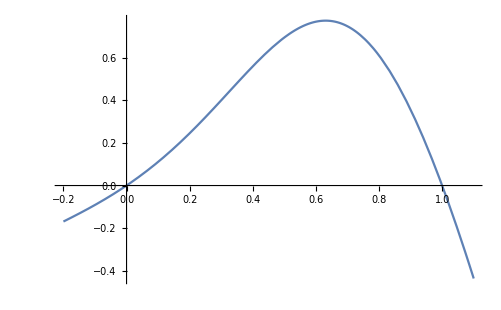

```mathematica
Plot[J[r], {r,-0.2,1.1}]
```

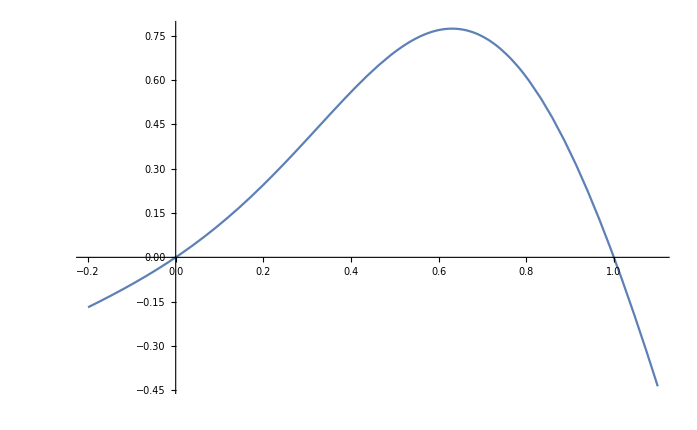

```mathematica
Show[%39,PlotLabel->None,LabelStyle->{9,GrayLevel[0]}]
```

```mathematica
FindMaximum[J[r], {r, 0,1}]
```

{0.773388,{r→0.630776}}

```mathematica
FindMaximum[D[r^2/(r^2-r+1),r], {r,0,1}]
```

{1.47049,{r→0.652704}}

```mathematica
FindMaximum[J11[r], {r, 0,1}]
```

{0.25,{r→0.5}}

```mathematica
FindMaximum[J12[r], {r, 0,1}]
```

{0.191603,{r→0.638897}}

```mathematica
FindMaximum[J21[r], {r, 0,1}]
```

{0.191603,{r→0.638897}}

```mathematica
FindMaximum[J22[r], {r, 0,1}]
```

{0.164891,{r→0.697225}}

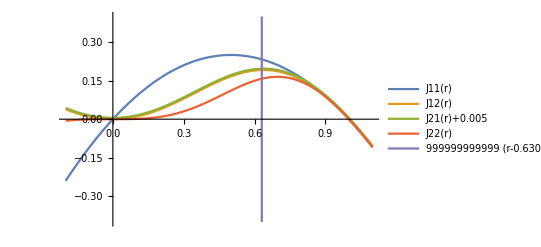

```mathematica
Plot[{J11[r], J12[r], J21[r]+ 0.005, J22[r], 999999999999*(r-0.6307757347525865)},{r,-0.2, 1.1}, PlotLegends->"Expressions" , PlotRange->0.4]
```